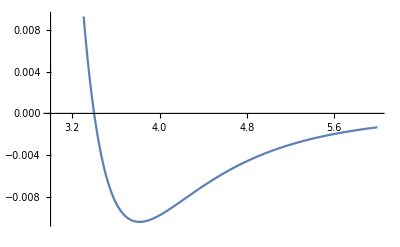

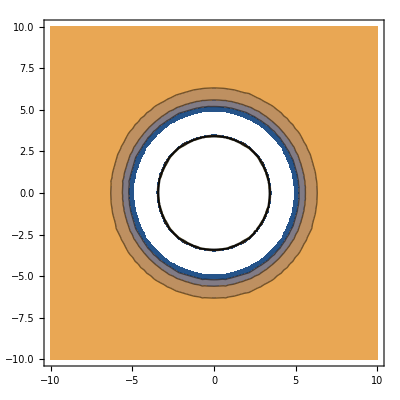

```mathematica
W[r_]=4 ϵ((σ/r)^12-(σ/r)^6);
Wv[x1_,x2_]:=W[EuclideanDistance[x1,x2]]
(* A point in space of molecule configurations is X={x1, y1, z1, x2, y2, z2, ...} *)
Ws[X_]:=Sum[Wv[X[[i]],X[[j]]],{i,1,Length[X]},{j,i+1,Length[X]}];

ϵ = 0.0104;
σ=3.40;
Plot[W[r],{r,3,6}]
ContourPlot[Wv[{0,0,0},{x,y,0}],{x,-10,10},{y,-10,10}]
```

```mathematica
CaptainKirk[n_]:=(
Reap[Sow[{0.0,0.,0.}];
If[n>1,
Sow[{x[2],0.,0.}];
];
If[n>2,
Sow[{x[3],y[3],0}];
];
If[n>3,
Do[Sow[{x[i],y[i],z[i]}],{i,4,n}];
]
][[2,1]]
)
Bones[n_]:=(
Reap[
Sow[{x[2],σ,.1 σ, 10n σ}];
If[n>2,
Sow[{x[3],σ,.1 σ, 10n σ}];
Sow[{y[3],σ,.1 σ, 10n σ}];
];

If[n>3,
start={σ,σ,σ};
Do[
Do[
Sow[{{x[i],y[i],z[i]}[[j]],start[[j]],.1σ,5 start[[j]]}];
,{j,{1,2,3}}];
start[[Mod[i-1,3]+1]]+=σ;
,{i,4,n}]
]
][[2,1]]
)
```

```mathematica
enterp=Scale[Import["enterp4.3ds","GraphicsComplex",Lighting->{{"Directional", White, {0, 0, 3}}},ImageSize->Automatic],.3];
```

```mathematica
Engage[n_]:=Module[
{sol=FindMinimum[
Ws[CaptainKirk[n]],Bones[n]
 ]},
{Show[Graphics3D[Translate[enterp,#/.sol[[2]]],Axes->True]&/@CaptainKirk[n]],sol[[1]]}
]
```

```mathematica
Quiet[Engage[#]&/@Range[2,6]]
```

{{-Graphics3D-,-0.0104},{-Graphics3D-,-0.0312},{-Graphics3D-,-0.0624},{-Graphics3D-,-0.0946801},{-Graphics3D-,-0.12795}}